```mathematica
∫_0^∞ Sin[x]/x ⅆx
```

π/2

```mathematica
{a,b}.{c,d}
```

a c+b d

```mathematica
Norm@{a,b}
```

√(Abs[a]^2+Abs[b]^2)

```mathematica
FullSimplify[
Norm@{a,b},{a,b}∈Reals]
```

√(a^2+b^2)

```mathematica
√({a,b}.{a,b})
```

√(a^2+b^2)

```mathematica
FullSimplify[
Abs[{a,b}.{c,d}]== Norm@{a,b} Norm@{c,d},{a,b,c,d}∈Reals]
```

b c==a d

```mathematica
FullSimplify[
Abs[{a,b}.{c,d}]≤ Norm@{a,b} Norm@{c,d},{a,b,c,d}∈Reals]
```

Abs[a c+b d]≤√((a^2+b^2) (c^2+d^2))

```mathematica
f[x_,y_]:={-y,x}
```

```mathematica
f[x,y]^2
```

{y^2,x^2}

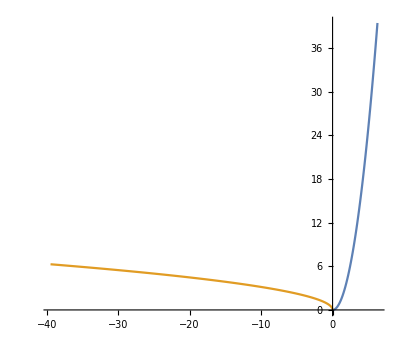

```mathematica
ParametricPlot[{
{t,t^2},
{-t^2,t}
},{t,0,2π}]
```

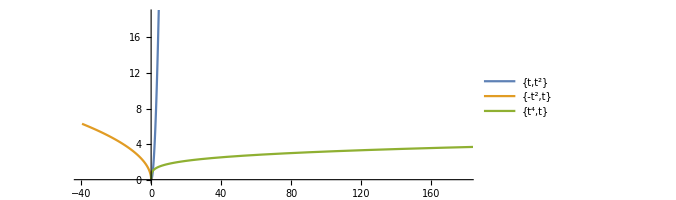

```mathematica
ParametricPlot[{
{t,t^2},
{-t^2,t},
{t^4,t}
},{t,0,2π},
PlotLegends->"Expressions"]
```

```mathematica
Re[a]
```

Re[a]

```mathematica
Re[a+b ⅈ]
```

-Im[b]+Re[a]

```mathematica
Im[a+b ⅈ]
```

Im[a]+Re[b]

```mathematica
f[a,b]
```

{-b,a}

```mathematica
Apply[f,{a,b}]
```

{-b,a}

```mathematica
Apply[
Composition[f]
,{a,b}]
```

{-b,a}

```mathematica
Apply[
Composition[f,f]
,{a,b}]
```

f[{-b,a}]

```mathematica
f@f[a,b]
```

f[{-b,a}]

```mathematica
f@@f[a,b]
```

{-a,-b}

```mathematica
f[a,b].f[c,d]
```

a c+b d

```mathematica
f[a,b].{a,b}
```

0

```mathematica
Re[a]+Im[bⅈ]
```

Im[bⅈ]+Re[a]

```mathematica
Re[a]+Im[b]
```

Im[b]+Re[a]

```mathematica
Plot3D[Im[b]+Re[a],{a,-10.,10.},{b,-10.,10.}]
```

-Graphics3D-

```mathematica
Conjugate[Re[a]+Im[b]]
```

Im[b]+Re[a]

```mathematica
Conjugate[a+b ⅈ]
```

Conjugate[a]-ⅈ Conjugate[b]

```mathematica
Conjugate[a+b ⅈ]==Conjugate[a]-ⅈ Conjugate[b]
```

True

```mathematica
Norm[a+b ⅈ]
```

Norm[a+ⅈ b]

```mathematica
Abs[a+b ⅈ]
```

Abs[a+ⅈ b]

```mathematica
Table[Subscript[a, i][t],{i,1,3,1}]
```

{a_1[t],a_2[t],a_3[t]}

```mathematica
D[{Subscript[a, 1][t],Subscript[a, 2][t],Subscript[a, 3][t]},t]
```

{a_1'[t],a_2'[t],a_3'[t]}

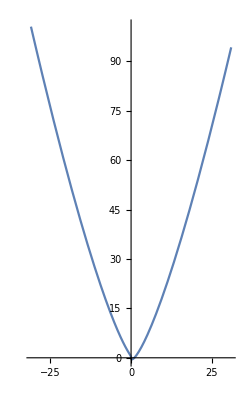

```mathematica
ParametricPlot[{
{t^3,t(t^3-1)}
},{t,-π,π}]
```

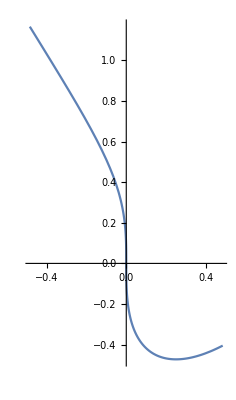

```mathematica
ParametricPlot[{
{t^3,t(t^3-1)}
},{t,-π/4,π/4}]
```

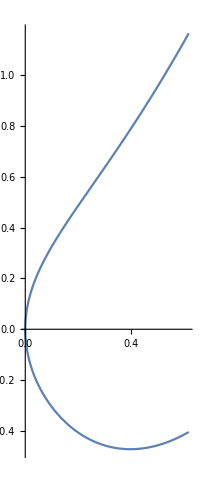

```mathematica
ParametricPlot[{
{t^2,t(t^3-1)}
},{t,-π/4,π/4}]
```

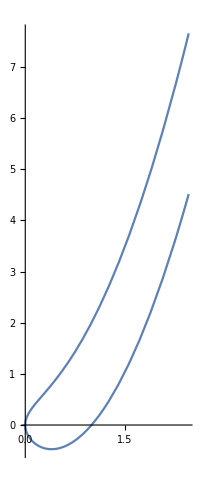

```mathematica
ParametricPlot[{
{t^2,t(t^3-1)}
},{t,-π/2,π/2}]
```

```mathematica
ParametricPlot[{
{t^2,t(t^3-1)},
{2t,D[t(t^3-1),t]}
},{t,-π/2,π/2}]
```

-Graphics-

```mathematica
D[{t^2,t(t^3-1)},t]
```

{2 t,-1+4 t^3}

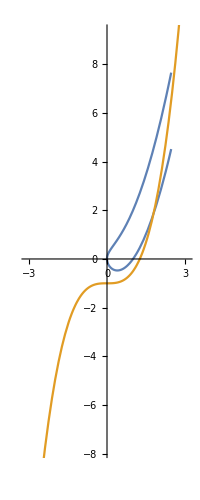

```mathematica
ParametricPlot[{
{t^2,t(t^3-1)},
{2 t,-1+4 t^3}
},{t,-π/2,π/2}]
```

```mathematica
Manipulate[
ParametricPlot[{
{t^2,t(t^3-1)},
{2 t,-1+4 t^3}
},{t,a,a+π/2}],
{a,0,10}]
```

```mathematica
Manipulate[
ParametricPlot[{
{t^2,t(t^3-1)},
{2 t,-1+4 t^3}
},{t,a,a+π/2}],
{a,0,10}]
```

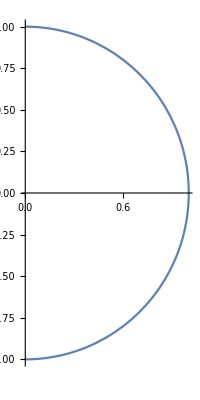

```mathematica
ParametricPlot[{
{Cos[t],Sin[t]}
},{t,-π/2,π/2}]
```



```mathematica
ParametricPlot[{
{Cos[t],Sin[t]}
},{t,0,2π}]
```

```mathematica
ParametricPlot[{
{Cos[t],Sin[t]}
},{t,0,2π}]
```

```mathematica
D[{Cos[t],Sin[t]},t]
```

{-Sin[t],Cos[t]}

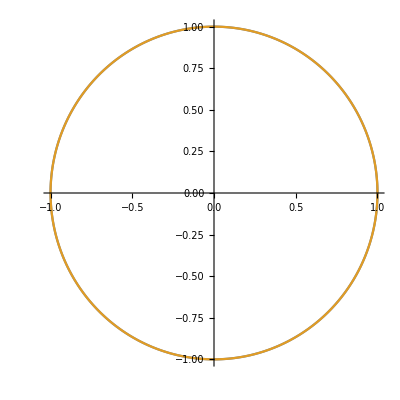

```mathematica
ParametricPlot[{
{Cos[t],Sin[t]},
{-Sin[t],Cos[t]}
},{t,0,2π}]
```

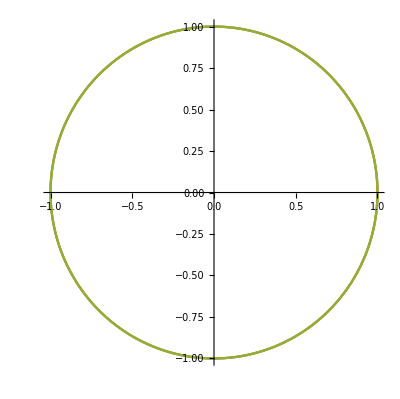

```mathematica
ParametricPlot[{
{Cos[t],Sin[t]},
{-Sin[t],Cos[t]},
{-Cos[t],-Sin[t]}
},{t,0,2π}]
```

```mathematica
With[{x=Cos[t],y=Sin[t]},
With[{diff=D[{x,y},t]},
With[{J=f[diff[[1]]]},
ParametricPlot[{
{x,y},
diff,
J
},{t,0,2π}]
]]]
```

-Graphics-

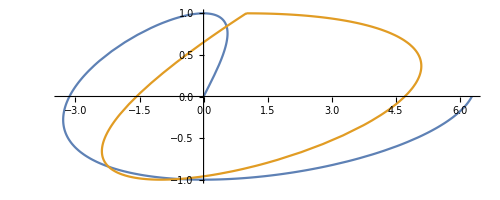

```mathematica
With[{x=t Cos[t],y=Sin[t]},
With[{diff=D[{x,y},t]},
With[{J=f[diff[[1]]]},
ParametricPlot[{
{x,y},
diff,
J
},{t,0,2π}]
]]]
```

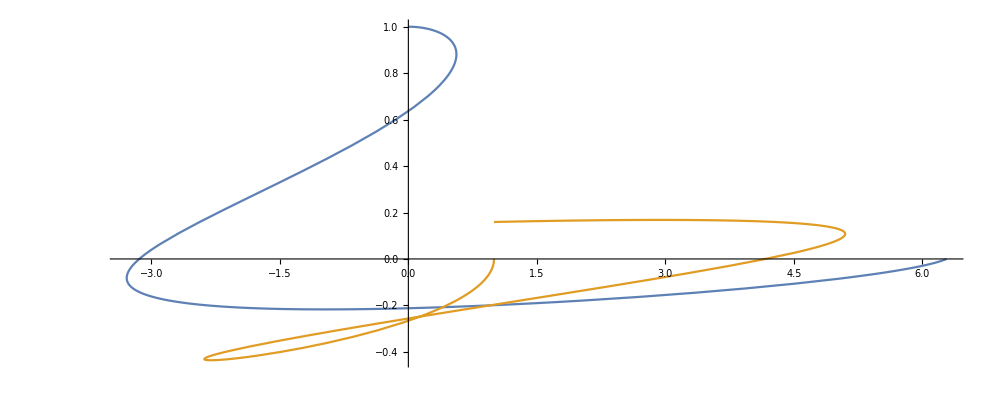

```mathematica
With[{x=t Cos[t],y=Sin[t]/t},
With[{diff=D[{x,y},t]},
With[{J=f[diff[[1]]]},
ParametricPlot[{
{x,y},
diff,
J
},{t,0,2π}]
]]]
```

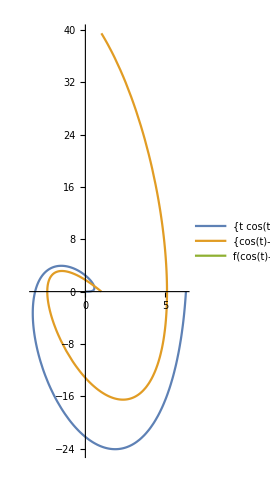

```mathematica
With[{x=t Cos[t],y=t^2 Sin[t]},
With[{diff=D[{x,y},t]},
With[{J=f[diff[[1]]]},
ParametricPlot[{
{x,y},
diff,
J
},{t,0,2π},PlotLegends->"Expressions"]
]]]
```

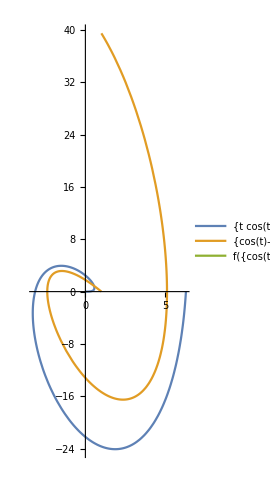

```mathematica
With[{x=t Cos[t],y=t^2 Sin[t]},
With[{diff=D[{x,y},t]},
With[{J=f[diff]},
ParametricPlot[{
{x,y},
diff,
J
},{t,0,2π},PlotLegends->"Expressions"]
]]]
```

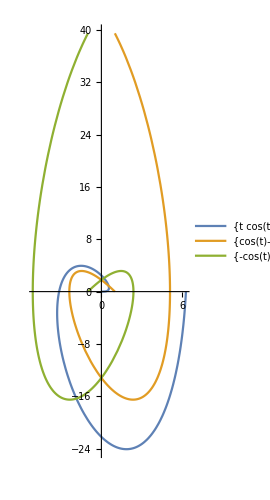

```mathematica
With[{x=t Cos[t],y=t^2 Sin[t]},
With[{diff=D[{x,y},t]},
With[{J={-diff[[1]],diff[[2]]}},
ParametricPlot[{
{x,y},
diff,
J
},{t,0,2π},PlotLegends->"Expressions"]
]]]
```

```mathematica
Manipulate[
ParametricPlot[{{
(1-a)(t Cos[t])+a(Cos[t]),
(1-a)(t^2 Sin[t])+a(Sin[t])
}},{t,0,2π}],{a,0,1}]
```

```mathematica
Manipulate[
ParametricPlot[{{
(1-a)(t Cos[t])+a(Cos[t]),
(1-a)(t^2 Sin[t])+a(Sin[t])
}},{t,0,2π},
PlotRange->{-25,5}],
{a,0,1}]
```

```mathematica
{Cos[t],Sin[t]}=={0,0}
```

{Cos[t],Sin[t]}=={0,0}

```mathematica
Reduce[{Cos[t],Sin[t]}=={0,0}]
```

Cos[t]==0&&Sin[t]==0

```mathematica
{a,b}.{a,b}
```

a^2+b^2

```mathematica
Plot3D[a^2+b^2,{a,-0.5485147527566367,0.5485147527566367},{b,-0.5485147527566367,0.5485147527566367}]
```

-Graphics3D-

```mathematica
N
```

```mathematica
Parame
```

Parame

```mathematica
ParametricPlot3D[{
{Cos[t],Sin[t],t},
},{t,0,2π}]
```

-Graphics3D-

```mathematica
D[{Cos[t],Sin[t]},1]
```

∂_1 {Cos[t],Sin[t]}

```mathematica
D[{Cos[t],Sin[t]},t]
```

{-Sin[t],Cos[t]}

```mathematica
Norm[D[{Cos[t],Sin[t]},t]]
```

√(Abs[Cos[t]]^2+Abs[Sin[t]]^2)

```mathematica
FullSimplify[
Norm[D[{Cos[t],Sin[t]},t]],t∈Reals]
```

1

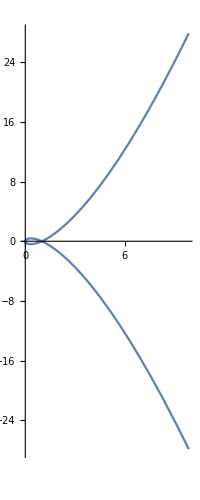

```mathematica
ParametricPlot[{
{t^2,t(t^2-1)}
},{t,-π,π}]
```

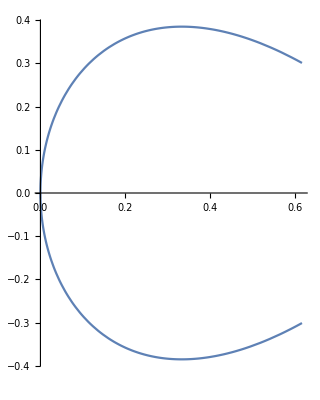

```mathematica
ParametricPlot[{
{t^2,t(t^2-1)}
},{t,-π/4,π/4}]
```

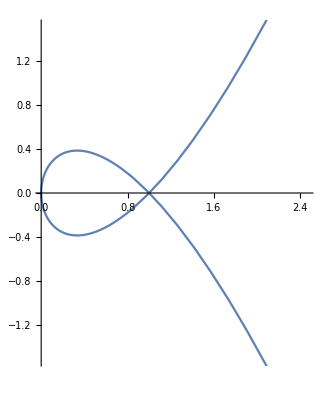

```mathematica
ParametricPlot[{
{t^2,t(t^2-1)}
},{t,-π/2,π/2}]
```

```mathematica
D[{t^2,t(t^2-1)},t]
```

{2 t,-1+3 t^2}

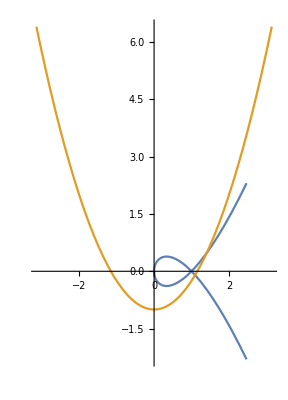

```mathematica
ParametricPlot[{
{t^2,t(t^2-1)},
{2 t,-1+3 t^2}
},{t,-π/2,π/2}]
```

```mathematica
√({2 t,-1+3 t^2}.{2 t,-1+3 t^2})
```

√(4 t^2+(-1+3 t^2)^2)

```mathematica
Simplify[√(4 t^2+(-1+3 t^2)^2)]
```

√(1-2 t^2+9 t^4)

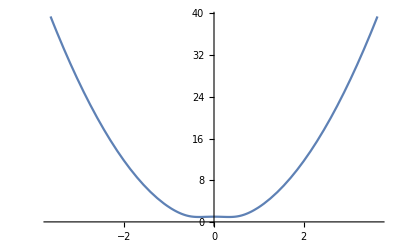

```mathematica
Plot[√(1-2 t^2+9 t^4),{t,-3.64,3.64}]
```

```mathematica
FullSimplify[
Normalize@{2 t,-1+3 t^2},t∈Reals]
```

{(2 t)/(√(1-2 t^2+9 t^4)),(-1+3 t^2)/(√(1-2 t^2+9 t^4))}

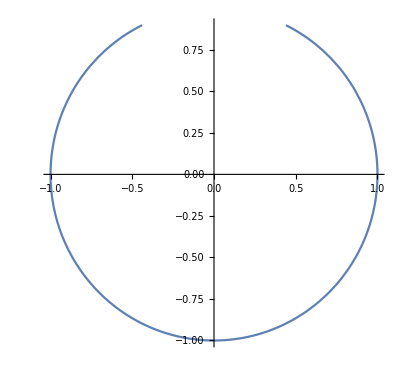

```mathematica
ParametricPlot[{
{(2 t)/(√(1-2 t^2+9 t^4)),(-1+3 t^2)/(√(1-2 t^2+9 t^4))}
},{t,-π/2,π/2}]
```

```mathematica
Norm[{(2 t)/(√(1-2 t^2+9 t^4)),(-1+3 t^2)/(√(1-2 t^2+9 t^4))}.{(2 t)/(√(1-2 t^2+9 t^4)),(-1+3 t^2)/(√(1-2 t^2+9 t^4))}]
```

Norm[(4 t^2)/(1-2 t^2+9 t^4)+((-1+3 t^2)^2)/(1-2 t^2+9 t^4)]

```mathematica
FullSimplify[
Sqrt[{(2 t)/(√(1-2 t^2+9 t^4)),(-1+3 t^2)/(√(1-2 t^2+9 t^4))}.{(2 t)/(√(1-2 t^2+9 t^4)),(-1+3 t^2)/(√(1-2 t^2+9 t^4))}],t∈Reals]
```

1

```mathematica
√((x'[t]/x'[t])^2+(y'[t]/x'[t])^2)
```

√(1+y'[t]^2/x'[t]^2)

```mathematica
Norm@{x[t],y[t]}
```

√(Abs[x[t]]^2+Abs[y[t]]^2)

```mathematica
FullSimplify[
√Norm[{x[t],y[t]}],{t,x[t],y[t]}∈Reals]
```

(x[t]^2+y[t]^2)^(1/4)

```mathematica
∫_0^(2π) (x[t]^2+y[t]^2)^(1/4)ⅆt
```

∫_0^(2 π) (x[t]^2+y[t]^2)^(1/4)ⅆt

```mathematica
With[{x=Cos,y=Sin},
∫_0^(2π) (x[t]^2+y[t]^2)^(1/4)ⅆt
]
```

2 π

```mathematica
MatrixForm[{x[t+α],y[t+β]}=={x[t]+∫_t^(t+α) x'[t]ⅆt,y[t]+∫_t^(t+β) y'[t]ⅆt}]
```

{x[t+α],y[t+β]}=={∫_t^(t+α) x'[t]ⅆt+x[t],∫_t^(t+β) y'[t]ⅆt+y[t]}

```mathematica
MatrixForm[{x[t+α],y[t+β]}]==MatrixForm[{x[t]+∫_t^(t+α) x'[t]ⅆt,y[t]+∫_t^(t+β) y'[t]ⅆt}]
```

(x[t+α]
y[t+β])==(∫_t^(t+α) x'[t]ⅆt+x[t]
∫_t^(t+β) y'[t]ⅆt+y[t])

```mathematica
Clear[f];f[x+α]==f[x]+∫_x^(x+α) f'[x]ⅆx
```

f[x+α]==f[x]+∫_x^(x+α) f'[x]ⅆx

```mathematica
With[{f=Identity},
f[x+α]==f[x]+∫_x^(x+α) f'[x]ⅆx
]
```

True

```mathematica
(x+α)^2==x^2+λ(2x)
```

(x+α)^2==x^2+2 x λ

```mathematica
(x+α)^2==x^2+α(2x)
```

(x+α)^2==x^2+2 x α

```mathematica
f[x+α]==f[x]+∫_x^(x+α) f'[x]ⅆx==f[x]+λ f'[x]
```

f[x+α]==f[x]+∫_x^(x+α) f'[x]ⅆx==f[x]+λ f'[x]

```mathematica
DSolve[f[x+α]==f[x]+∫_x^(x+α) f'[x]ⅆx==f[x]+λ f'[x],{f[x]},{x}]
```

DSolve[f[x+α]==f[x]+∫_x^(x+α) f'[x]ⅆx==f[x]+λ f'[x],{f[x]},{x}]

```mathematica
f[x]+∫_x^(x+α) f'[x]ⅆx==f[x]+λ f'[x]
```

f[x]+∫_x^(x+α) f'[x]ⅆx==f[x]+λ f'[x]

```mathematica
DSolve[f[x]+∫_x^(x+α) f'[x]ⅆx==f[x]+λ f'[x],{f[x]},{x}]
```

DSolve[f[x]+∫_x^(x+α) f'[x]ⅆx==f[x]+λ f'[x],{f[x]},{x}]

```mathematica
Solve[f[x]+∫_x^(x+α) f'[x]ⅆx==f[x]+λ f'[x],{λ}]
```

{{λ→(∫_x^(x+α) f'[x]ⅆx)/f'[x]}}

```mathematica
λ/.{{λ->(∫_x^(x+α) f'[x]ⅆx)/f'[x]}}
```

{(∫_x^(x+α) f'[x]ⅆx)/f'[x]}

```mathematica
First[{(∫_x^(x+α) f'[x]ⅆx)/f'[x]}]
```

(∫_x^(x+α) f'[x]ⅆx)/f'[x]

```mathematica
With[{x=#^2&},
(∫_x^(x+α) f'[x]ⅆx)/f'[x]]
```

(∫_(#1^2&)^(α+(#1^2&)) f'[#1^2&]ⅆ(#1^2&))/f'[#1^2&]

```mathematica
With[{x=Function[i,i^2]},
(∫_x^(x+α) f'[x]ⅆx)/f'[x]]
```

(∫_Function[i,i^2]^(α+Function[i,i^2]) f'[Function[i,i^2]]ⅆFunction[i,i^2])/f'[Function[i,i^2]]

```mathematica
(f[x+α]-f[x])/f'[x]
```

(-f[x]+f[x+α])/f'[x]

```mathematica
With[{f=Log},
(f[x+α]-f[x])/f'[x]]
```

x (-Log[x]+Log[x+α])

```mathematica
Manipulate[Plot[x (-Log[x]+Log[x+α]),{x,-3.331680831882222,272.28586232849005}],{α,-4.998760623911667,206.71439674636756}]
```

```mathematica
x (-Log[x]+Log[x+10])
```

x (-Log[x]+Log[10+x])

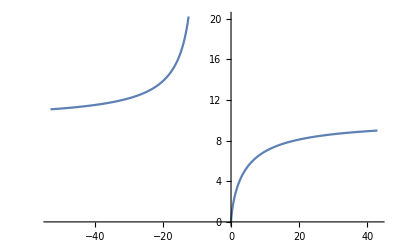

```mathematica
Plot[x (-Log[x]+Log[10+x]),{x,-53.,43.}]
```

```mathematica
f[x]+λ f'[x]
```

```mathematica
f[x+α]==f[x]+λ f'[x]
```

f[x+α]==f[x]+λ f'[x]

```mathematica
DSolve[f[x+α]==f[x]+λ f'[x],{f[x]},{x}]
```

DSolve[f[x+α]==f[x]+λ f'[x],{f[x]},{x}]

```mathematica
Solve[f[x+α]==f[x]+λ f'[x],λ]
```

{{λ→(-f[x]+f[x+α])/f'[x]}}

```mathematica
(f[x+α]-f[x])/f'[x]
```

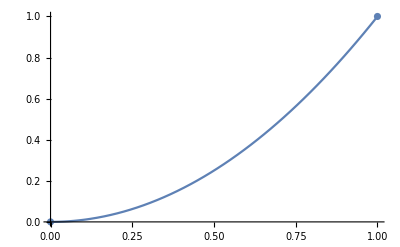

```mathematica
Show[{
Plot[x^2,{x,0,1}],
ListPlot[{{0,0},{1,1}}]}]
```

```mathematica
Solve[(x+1)^2==x^2+λ 2x,λ]
```

{{λ→(1+2 x)/(2 x)}}

```mathematica
(1+2 x)/(2 x)
```

(1+2 x)/(2 x)

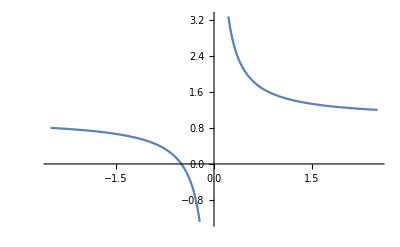

```mathematica
Plot[(1+2 x)/(2 x),{x,-2.5024999999999995,2.5024999999999995}]
```

```mathematica
(1+2 x)/(2 x)2x
```

1+2 x

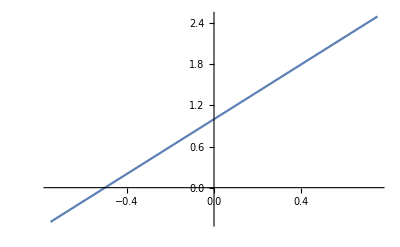

```mathematica
Plot[1+2 x,{x,-0.75,0.75}]
```

```mathematica
Solve[(x+1)==x+λ,λ]
```

{{λ→1}}

```mathematica
Solve[(x+α)==x+λ,λ]
```

{{λ→α}}

```mathematica
Solve[(x+α)^2==x^2+λ 2x,λ]
```

{{λ→(2 x α+α^2)/(2 x)}}

```mathematica
Γ[x,α,f[x],f'[x]]
```

```mathematica
Solve[f[x+α]==f[x]+λ f'[x],λ]
```

{{λ→(-f[x]+f[x+α])/f'[x]}}

```mathematica
Γ[x,f[x],f'[x],α]==λ
```

```mathematica
f[x-α]-f[x]==α
```

```mathematica
Solve[Log[x+α]==Log[x]+λ Log'[x],λ]
```

{{λ→-x (Log[x]-Log[x+α])}}

```mathematica
With[{α=1,f=Log},
Solve[f[x+α]==f[x]+λ f'[x],λ]
]
```

{{λ→-x (Log[x]-Log[1+x])}}

```mathematica
λ/.{{λ->-x (Log[x]-Log[1+x])}}
```

{-x (Log[x]-Log[1+x])}

```mathematica
First[{-x (Log[x]-Log[1+x])}]
```

-x (Log[x]-Log[1+x])

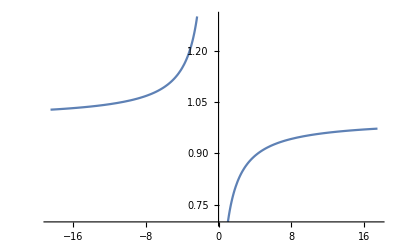

```mathematica
Plot[-x (Log[x]-Log[1+x]),{x,-18.5,17.5}]
```

```mathematica
{{λ->-x (Log[x]-Log[1+x])}}/.Rule->Equal
```

{{λ==-x (Log[x]-Log[1+x])}}

```mathematica
Γ[x,f[x],f'[x],α]==f[x]==λ
```

Γ[x,f[x],f'[x],α]==f[x]==λ

```mathematica
(-f[x]+f[x+α])/f'[x]==f[x]
```

(-f[x]+f[x+α])/f'[x]==f[x]

```mathematica
DSolve[(-f[x]+f[x+α])/f'[x]==f[x],{f[x]},{x}]
```

DSolve[(-f[x]+f[x+α])/f'[x]==f[x],{f[x]},{x}]

```mathematica
(-f[x]+f[x+1])/f'[x]==f[x]
```

(-f[x]+f[1+x])/f'[x]==f[x]

```mathematica
DSolve[(-f[x]+f[1+x])/f'[x]==f[x],{f[x]},{x}]
```

DSolve[(-f[x]+f[1+x])/f'[x]==f[x],{f[x]},{x}]

```mathematica
(f[1+x]-f[x])/f'[x]==f[x]
```

(-f[x]+f[1+x])/f'[x]==f[x]

```mathematica
(-f[x]+f[x+α])/f'[x]==f[x]
```

(-f[x]+f[x+α])/f'[x]==f[x]

```mathematica
MultiplySides[(-f[x]+f[x+α])/f'[x]==f[x],f'[x]]
```

Piecewise[{{-f[x]+f[x+α]==f[x] f'[x], f'[x]≠0}, {(-f[x]+f[x+α])/f'[x]==f[x], True}}]

```mathematica
FullSimplify[
MultiplySides[(-f[x]+f[x+α])/f'[x]==f[x],f'[x]],
{x,α,f[x],f'[x]}∈Reals∧f'[x]≠0]
```

f[x+α]==f[x] (1+f'[x])

```mathematica
DSolve[f[x+α]==f[x] (1+f'[x]),{f[x]},{x}]
```

DSolve[f[x+α]==f[x] (1+f'[x]),{f[x]},{x}]

```mathematica
With[{f=Sin},
f[x+α]==f[x] (1+f'[x])
]
```

Sin[x+α]==(1+Cos[x]) Sin[x]

```mathematica
(1+Cos[x]) Sin[x]
```

(1+Cos[x]) Sin[x]

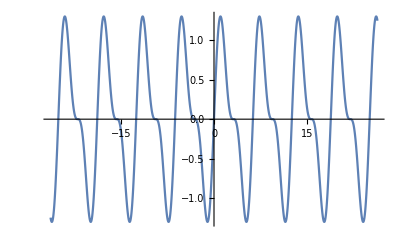

```mathematica
Plot[(1+Cos[x]) Sin[x],{x,-26.389378290154262,26.389378290154262}]
```

```mathematica
Plot3D[
(2 x α+α^2)/(2 x),
{x,-2,2},{α,0,10}]
```

-Graphics3D-

```mathematica
Plot3D[
(2 x α+α^2)/(2 x),
{x,-2,2},{α,0,10},PlotRange->Full]
```

-Graphics3D-

```mathematica
ParametricPlot[
{Cos[t],Sin[t]},
{t,0,2π}]
```

-Graphics-

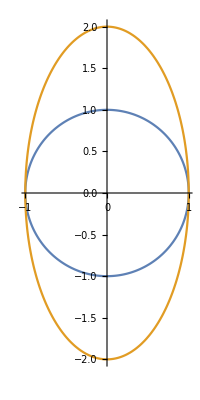

```mathematica
ParametricPlot[{
{Cos[t],Sin[t]},
{Cos[t],2Sin[t]}
},{t,0,2π}]
```

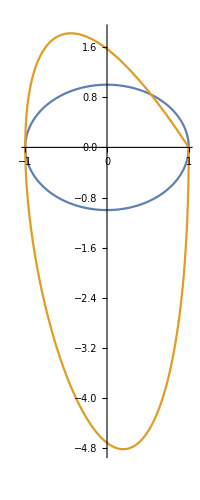

```mathematica
ParametricPlot[{
{Cos[t],Sin[t]},
{Cos[t],t Sin[t]}
},{t,0,2π}]
```

```mathematica
{Cos[t],t Sin[t]}/.t->1
```

{Cos[1],Sin[1]}

```mathematica
N@{Cos[1],Sin[1]}
```

{0.540302,0.841471}

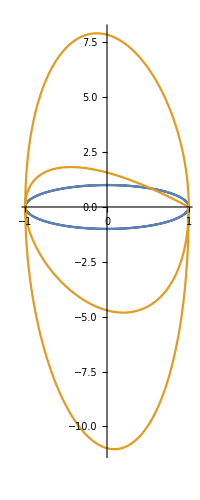

```mathematica
ParametricPlot[{
{Cos[t],Sin[t]},
{Cos[t],t Sin[t]}
},{t,0,4π}]
```

```mathematica
ParametricPlot[{
{Cos[t],Sin[t]},
{Cos[t],2Sin[t]}
},{t,0,2π}]
```

-Graphics-

```mathematica
Normalize@{Cos[t],Sin[t]}
```

{Cos[t]/(√(Abs[Cos[t]]^2+Abs[Sin[t]]^2)),Sin[t]/(√(Abs[Cos[t]]^2+Abs[Sin[t]]^2))}

```mathematica
FullSimplify[
Normalize@{Cos[t],Sin[t]},t∈Reals]
```

{Cos[t],Sin[t]}

```mathematica
FullSimplify[
Normalize@{Cos[t],Sin[t]}.
Normalize@{Cos[t],2Sin[t]},
t∈Reals]
```

(Cos[t]^2+2 Sin[t]^2)/(√(Cos[t]^2+4 Sin[t]^2))

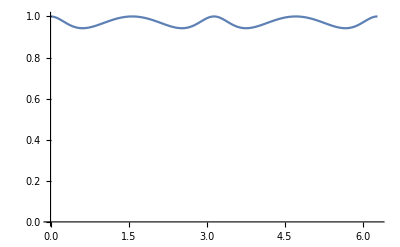

```mathematica
Plot[(Cos[t]^2+2 Sin[t]^2)/(√(Cos[t]^2+4 Sin[t]^2)),{t,0,2 π},PlotRange->{0,1}]
```

```mathematica
Integrate[{Cos[t],Sin[t]}.{Cos[t],Sin[t]},{t,0,1}]
```

1

```mathematica
(Cos[t]^2+2 Sin[t]^2)/(√(Cos[t]^2+4 Sin[t]^2))
```

```mathematica
Integrate[(Cos[t]^2+2 Sin[t]^2)/(√(Cos[t]^2+4 Sin[t]^2)),{t,0,1}]
```

1/3 (EllipticE[1,-3]+2 EllipticF[1,-3])

```mathematica
N[1/3 (EllipticE[1,-3]+2 EllipticF[1,-3])]
```

0.962359+0. ⅈ

```mathematica
"convert to exponential"0.9623587766771251+0. ⅈWith[{n=Abs[0.9623587766771251+0. ⅈ],a=Arg[0.9623587766771251+0. ⅈ]},Defer[n ⅇ^(ⅈ a)]]
```

0.962359 ⅇ^(ⅈ 0.)

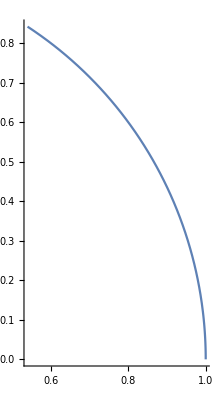

```mathematica
PolarPlot[1,{θ,0,1}]
```

```mathematica
PolarPlot[1,{θ,0,2π}]
```

-Graphics-

```mathematica
PolarPlot[1,{θ,0,2π}]
```

```mathematica
r[θ]=Identity;x=r[θ]Cos[θ];y=r[θ]Sin[θ]
```

```mathematica
y=1Sin[θ]
```

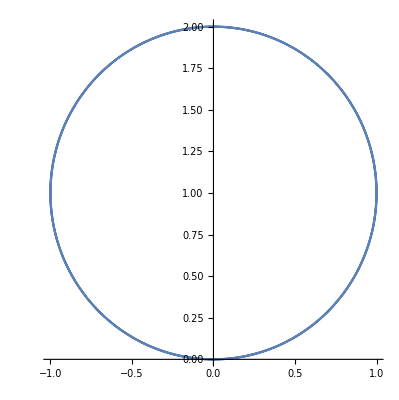

```mathematica
PolarPlot[2Sin[θ],{θ,0,2π}]
```

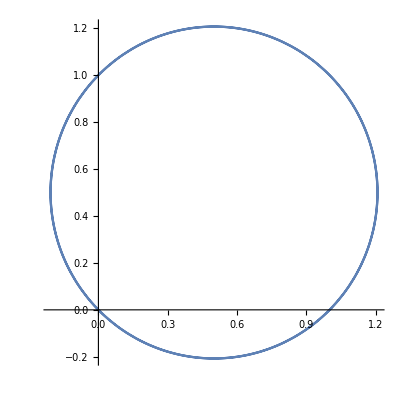

```mathematica
PolarPlot[Sin[θ]+Cos[θ],{θ,0,2π}]
```

```mathematica
Solve[x=r Cos[θ],r]
```

Solve[r Cos[θ],r]

```mathematica
Solve[x==r Cos[θ],r]
```

{{}}

```mathematica
r==√Norm[V[x[t],y[t]]]
```

r==√Norm[V[(r Cos[θ])[t],y[t]]]

```mathematica
Clear[x]
```

```mathematica
r==√Norm[V[x[t],y[t]]]
```

r==√Norm[V[x[t],y[t]]]

```mathematica
r==√Norm[{Cos[t],Sin[t]}]
```

r==(Abs[Cos[t]]^2+Abs[Sin[t]]^2)^(1/4)

```mathematica
FullSimplify[
r==√Norm[{Cos[t],2Sin[t]}],{r,t}∈Reals]
```

(Cos[t]^2+4 Sin[t]^2)^(1/4)==r

```mathematica
PolarPlot[2Sin[θ],{θ,0,2π}]
```

```mathematica
ArcTan[x]
```

ArcTan[x]

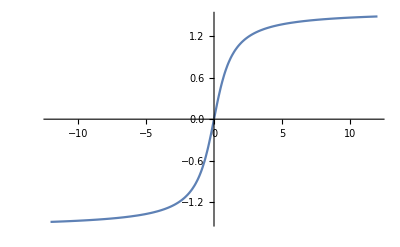

```mathematica
Plot[ArcTan[x],{x,-12.,12.}]
```

```mathematica
(Cos[t]^2+4 Sin[t]^2)^(1/4)==r
```

(Cos[t]^2+4 Sin[t]^2)^(1/4)==r

```mathematica
ArcTan[Cos[t],2Sin[t]]
```

ArcTan[Cos[t],2 Sin[t]]

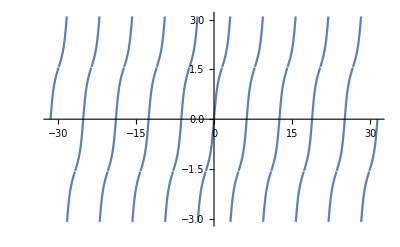

```mathematica
Plot[ArcTan[Cos[t],2 Sin[t]],{t,-10 π,10 π}]
```

```mathematica
ArcTan[(2 Sin[t])/Cos[t]]
```

ArcTan[2 Tan[t]]

```mathematica
θ==ArcTan[(2 Sin[t])/Cos[t]]
```

θ==ArcTan[2 Tan[t]]

```mathematica
Solve[θ==ArcTan[2 Tan[t]],{t}]
```

{{t→ConditionalExpression[ArcTan[Tan[θ]/2]+π C[1],((Re[θ]==-π/2&&Im[θ]<0)||-π/2<Re[θ]<π/2||(Re[θ]==π/2&&Im[θ]>0))&&C[1]∈ℤ]}}

```mathematica
FullSimplify[
Solve[θ==ArcTan[2 Tan[t]],{t}],θ∈Reals]
```

{{t→ConditionalExpression[ArcCot[2 Cot[θ]]+π C[1],-π/2<θ<π/2&&C[1]∈ℤ]}}

```mathematica
FullSimplify[
Solve[θ==ArcTan[2 Tan[t]],{t}],θ∈Reals∧-π/2<θ<π/2]
```

{{t→ConditionalExpression[ArcCot[2 Cot[θ]]+π C[1],C[1]∈ℤ]}}

```mathematica
ArcCot[2 Cot[θ]]+π
```

π+ArcCot[2 Cot[θ]]

```mathematica
(Cos[π+ArcCot[2 Cot[θ]]]^2+4 Sin[π+ArcCot[2 Cot[θ]]]^2)^(1/4)
```

(1/(1+Tan[θ]^2/4)+Tan[θ]^2/(1+Tan[θ]^2/4))^(1/4)

```mathematica
FullSimplify[(1/(1+Tan[θ]^2/4)+Tan[θ]^2/(1+Tan[θ]^2/4))^(1/4)]
```

2^(3/4) (1/(5+3 Cos[2 θ]))^(1/4)

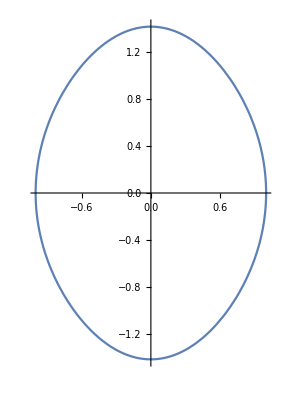

```mathematica
PolarPlot[(1/(1+Tan[θ]^2/4)+Tan[θ]^2/(1+Tan[θ]^2/4))^(1/4),{θ,0,2 π}]
```

```mathematica
2^(3/4) (1/(5+3 Cos[2 θ]))^(1/4)//FullForm
```

Times[Power[2,Rational[3,4]],Power[Power[Plus[5,Times[3,Cos[Times[2,\[Theta]]]]],-1],Rational[1,4]]]

```mathematica
PolarPlot[2^(3/4) (1/(5+3 Cos[2 θ]))^(1/4),{θ,0,2 π}]
```

-Graphics-

```mathematica
Times[Power[2,Rational[3,4]],Power[Power[Plus[5,Times[3,Cos[Times[2,\[Theta]]]]],-1],Rational[1,4]]]
```

2^(3/4) (1/(5+3 Cos[2 θ]))^(1/4)

```mathematica
{Identity,
```

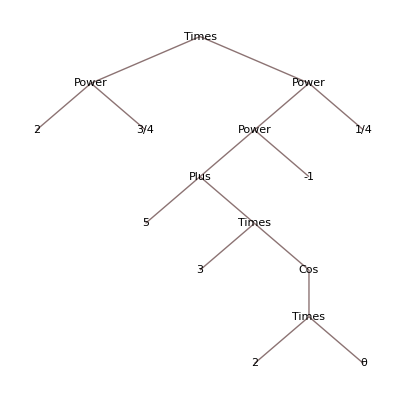

```mathematica
2^(3/4) (1/(5+3 Cos[2 θ]))^(1/4)//TreeForm
```

```mathematica
Times[2]
```

2

```mathematica
{Identity,2#&,Cos,3#&,#+5&,Power[#,-1]&,Power[#,1/4]&,Power[2,3/4]#&}
```

{Identity,2 #1&,Cos,3 #1&,#1+5&,1/#1&,#1^(1/4)&,2^(3/4) #1&}

```mathematica
ops={Identity,2 #1&,Cos,3 #1&,#1+5&,1/#1&,#1^(1/4)&,2^(3/4) #1&}
```

{Identity,2 #1&,Cos,3 #1&,#1+5&,1/#1&,#1^(1/4)&,2^(3/4) #1&}

```mathematica
Manipulate[
Apply[Composition,ops[[;;a]]],
{a,1,Length@ops,1}]
```

```mathematica
Manipulate[
With[{f=Apply[Composition,ops[[;;a]]]},
PolarPlot[f[θ],{θ,0,2π}]
],{a,1,Length@ops,1}]
```

```mathematica
Reverse@{Identity,2 #1&,Cos,3 #1&,#1+5&,1/#1&,#1^(1/4)&,2^(3/4) #1&}
```

{2^(3/4) #1&,#1^(1/4)&,1/#1&,#1+5&,3 #1&,Cos,2 #1&,Identity}

```mathematica
rev=Reverse@ops
```

{2^(3/4) #1&,#1^(1/4)&,1/#1&,#1+5&,3 #1&,Cos,2 #1&,Identity}

```mathematica
Manipulate[
With[{f=Apply[Composition,rev[[;;a]]]},
PolarPlot[f[θ],{θ,0,2π}]
],{a,1,Length@ops,1}]
```

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

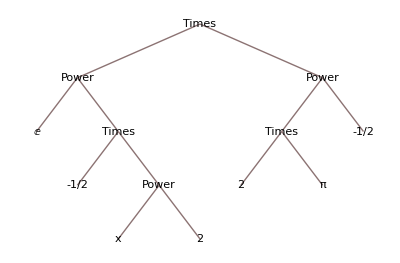

```mathematica
(ⅇ^(-x^2/2))/(√(2 π))//TreeForm
```

```mathematica
Reverse@{Identity,Power[#,2]&,-#/2&,Exp,Power[2π,-1/2]#&}
```

{(2 π)^(-1/2) #1&,Exp,-#1/2&,#1^2&,Identity}

```mathematica
Manipulate[
With[{f=Apply[Composition,Out[206][[;;a]]]},
Plot[f[x],{x,-3,3},PlotRange->{-1,1}]
],{a,1,Length@Out[206],1}]
```

```mathematica
Partition[{(2 π)^(-1/2) #1&,Exp,-#1/2&,#1^2&,Identity},2,1]
```

{{(2 π)^(-1/2) #1&,Exp},{Exp,-#1/2&},{-#1/2&,#1^2&},{#1^2&,Identity}}

```mathematica
(2 x α+α^2)/(2 x)/.α->1
```

(1+2 x)/(2 x)

```mathematica
Plot[(1+2 x)/(2 x),{x,-2.5024999999999995,2.5024999999999995}]
```

-Graphics-

```mathematica
(2 x α+α^2)/(2 x)/.α->1
```

```mathematica
1==∫_0^a √(1+4 x^2)ⅆx
```

ConditionalExpression[1==1/4 (2 a √(1+4 a^2)+ArcSinh[2 a]),Re[a]≠0||-1/2<Im[a]<0||0<Im[a]<1/2]

```mathematica
FullSimplify[
1==∫_0^a √(1+4 x^2)ⅆx,a∈Reals]
```

ConditionalExpression[2 a √(1+4 a^2)+ArcSinh[2 a]==4,a≠0]

```mathematica
FullSimplify[
1==∫_0^a √(1+4 x^2)ⅆx,a∈Reals∧a≠0]
```

2 a √(1+4 a^2)+ArcSinh[2 a]==4

```mathematica
Solve[2 a √(1+4 a^2)+ArcSinh[2 a]==4,{a}]
```

Solve[2 a √(1+4 a^2)+ArcSinh[2 a]==4,{a}]

```mathematica
FullSimplify[
1==∫_0^a √(1+f'[x]^2)ⅆx,a∈Reals∧a≠0]
```

∫_0^a √(1+f'[x]^2)ⅆx==1

```mathematica
Solve[∫_0^a √(1+f'[x]^2)ⅆx==1,{a}]
```

Solve[∫_0^a √(1+f'[x]^2)ⅆx==1,{a}]

```mathematica
dot[p,q]==p.q;norm==√dot[p,p];distance[p,q]==norm[p-q]
```

distance[p,q]==norm[p-q]

```mathematica
Norm@{x'[t],y'[t]}
```

√(Abs[x'[t]]^2+Abs[y'[t]]^2)

```mathematica
FullSimplify[
Norm@{x'[t],y'[t]},{t,x'[t],y'[t]}∈Reals]
```

√(x'[t]^2+y'[t]^2)

```mathematica
FullSimplify[
Normalize@{Cos[t],t Sin[t]},t∈Reals]
```

{Cos[t]/(√(Abs[t Sin[t]]^2+Cos[t]^2)),(t Sin[t])/(√(Abs[t Sin[t]]^2+Cos[t]^2))}

```mathematica
FullSimplify[
Normalize@{Cos[t],t Sin[t]},t∈Reals]
```

```mathematica
{Cos[t]/(√((t Sin[t])^2+Cos[t]^2)),(t Sin[t])/(√((t Sin[t])^2+Cos[t]^2))}
```

{Cos[t]/(√(Cos[t]^2+t^2 Sin[t]^2)),(t Sin[t])/(√(Cos[t]^2+t^2 Sin[t]^2))}

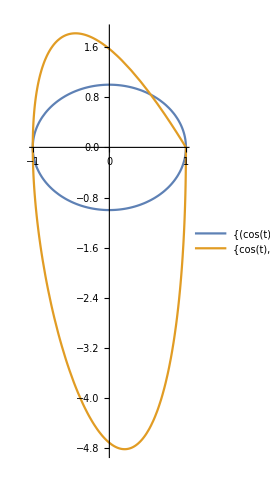

```mathematica
ParametricPlot[{
{Cos[t]/(√(Cos[t]^2+t^2 Sin[t]^2)),(t Sin[t])/(√(Cos[t]^2+t^2 Sin[t]^2))},
{Cos[t],t Sin[t]}
},{t,0,2π},PlotLegends->"Expressions"]
```

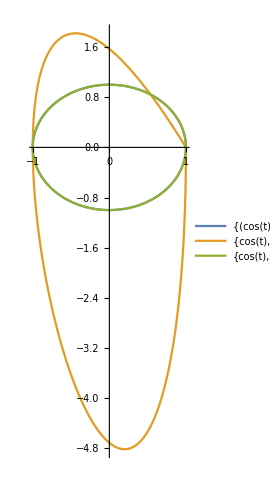

```mathematica
ParametricPlot[{
{Cos[t]/(√(Cos[t]^2+t^2 Sin[t]^2)),(t Sin[t])/(√(Cos[t]^2+t^2 Sin[t]^2))},
{Cos[t],t Sin[t]},
{Cos[t],Sin[t]}
},{t,0,2π},PlotLegends->"Expressions"]
```

```mathematica
D[{Cos[t]/(√(Cos[t]^2+t^2 Sin[t]^2)),(t Sin[t])/(√(Cos[t]^2+t^2 Sin[t]^2))},t]
```

{-(Cos[t] (-2 Cos[t] Sin[t]+2 t^2 Cos[t] Sin[t]+2 t Sin[t]^2))/(2 (Cos[t]^2+t^2 Sin[t]^2)^(3/2))-Sin[t]/(√(Cos[t]^2+t^2 Sin[t]^2)),-(t Sin[t] (-2 Cos[t] Sin[t]+2 t^2 Cos[t] Sin[t]+2 t Sin[t]^2))/(2 (Cos[t]^2+t^2 Sin[t]^2)^(3/2))+(t Cos[t])/(√(Cos[t]^2+t^2 Sin[t]^2))+Sin[t]/(√(Cos[t]^2+t^2 Sin[t]^2))}

```mathematica
PolynomialReduce[-(Cos[t] (-2 Cos[t] Sin[t]+2 t^2 Cos[t] Sin[t]+2 t Sin[t]^2))/(2 (Cos[t]^2+t^2 Sin[t]^2)^(3/2))-Sin[t]/(√(Cos[t]^2+t^2 Sin[t]^2)),{-(t Sin[t] (-2 Cos[t] Sin[t]+2 t^2 Cos[t] Sin[t]+2 t Sin[t]^2))/(2 (Cos[t]^2+t^2 Sin[t]^2)^(3/2))+(t Cos[t])/(√(Cos[t]^2+t^2 Sin[t]^2))+Sin[t]/(√(Cos[t]^2+t^2 Sin[t]^2))},Hold[t]]
```

{{(-(t^2 Cos[t]^2 Sin[t])/(Cos[t]^2+t^2 Sin[t]^2)-(t Cos[t] Sin[t]^2)/(Cos[t]^2+t^2 Sin[t]^2)-(t^2 Sin[t]^3)/(Cos[t]^2+t^2 Sin[t]^2))/(t Cos[t]+Sin[t]+(t Cos[t] Sin[t]^2)/(Cos[t]^2+t^2 Sin[t]^2)-(t^3 Cos[t] Sin[t]^2)/(Cos[t]^2+t^2 Sin[t]^2)-(t^2 Sin[t]^3)/(Cos[t]^2+t^2 Sin[t]^2))},0}

```mathematica
{-(Cos[t] (-2 Cos[t] Sin[t]+2 t^2 Cos[t] Sin[t]+2 t Sin[t]^2))/(2 (Cos[t]^2+t^2 Sin[t]^2)^(3/2))-Sin[t]/(√(Cos[t]^2+t^2 Sin[t]^2)),-(t Sin[t] (-2 Cos[t] Sin[t]+2 t^2 Cos[t] Sin[t]+2 t Sin[t]^2))/(2 (Cos[t]^2+t^2 Sin[t]^2)^(3/2))+(t Cos[t])/(√(Cos[t]^2+t^2 Sin[t]^2))+Sin[t]/(√(Cos[t]^2+t^2 Sin[t]^2))}
```

{-(Cos[t] (-2 Cos[t] Sin[t]+2 t^2 Cos[t] Sin[t]+2 t Sin[t]^2))/(2 (Cos[t]^2+t^2 Sin[t]^2)^(3/2))-Sin[t]/(√(Cos[t]^2+t^2 Sin[t]^2)),-(t Sin[t] (-2 Cos[t] Sin[t]+2 t^2 Cos[t] Sin[t]+2 t Sin[t]^2))/(2 (Cos[t]^2+t^2 Sin[t]^2)^(3/2))+(t Cos[t])/(√(Cos[t]^2+t^2 Sin[t]^2))+Sin[t]/(√(Cos[t]^2+t^2 Sin[t]^2))}

```mathematica
{(2 π)^(-1/2) #1&,Exp,-#1/2&,#1^2&}
```

{(2 π)^(-1/2) #1&,Exp,-#1/2&,#1^2&}

```mathematica
Partition[Out[228],2,1]
```

{{(2 π)^(-1/2) #1&,Exp},{Exp,-#1/2&},{-#1/2&,#1^2&}}

```mathematica
Table[
```

```mathematica
{(2 π)^(-1/2) #1&,Exp,-#1/2&,#1^2&,Identity}
```

{(2 π)^(-1/2) #1&,Exp,-#1/2&,#1^2&,Identity}

```mathematica
Partition[Out[230],2,1]
```

{{(2 π)^(-1/2) #1&,Exp},{Exp,-#1/2&},{-#1/2&,#1^2&},{#1^2&,Identity}}

```mathematica
Reverse@{(2 π)^(-1/2) #1&,Exp,-#1/2&,#1^2&,Identity}
```

{Identity,#1^2&,-#1/2&,Exp,(2 π)^(-1/2) #1&}

```mathematica
Partition[Out[232],2,1]
```

{{Identity,#1^2&},{#1^2&,-#1/2&},{-#1/2&,Exp},{Exp,(2 π)^(-1/2) #1&}}

```mathematica
Map[
Function[pair,
Manipulate[
Plot[
(1-a)First[pair]+a Last[pair],
{x,-2,2},
PlotRange->{0,1}]
,{a,0,1}]
],Out[233]]
```

{,,,}

```mathematica
Grid@
Map[
Function[pair,
Manipulate[
Plot[
(1-a)First[pair]+a Last[pair],
{x,-2,2},
PlotRange->{0,1}]
,{a,0,1}]
],Out[233]]
```

Grid[{,,,}]

```mathematica
Map[
Manipulate[
Plot[
(1-a)First[#]+a Last[#],
{x,-2,2}]
,{a,0,1}]&
,Out[233]]
```

{,,,}

```mathematica
Manipulate[
Plot[
(1-a)First[Out[233][[b]]]+a Last[Out[233][[b]]],
{x,-2,2}],
{a,0,1},{b,1,Length@Out[233]}]
```

```mathematica
{{x,x^2},{x^2,-x/2},{-x/2,Exp[x]},{Exp[x],(2 π)^(-1/2) x}}
```

{{x,x^2},{x^2,-x/2},{-x/2,ⅇ^x},{ⅇ^x,x/(√(2 π))}}

```mathematica
Manipulate[
Plot[
(1-a)First[b]+a Last[b],
{x,-2,2},PlotRange->{0,1}],
{a,0,1},{b,Out[241]}]
```

```mathematica
Manipulate[
With[{f=First[b],g=Last[b]},
Plot[
(1-a)f+a g,
{x,-2,2},PlotRange->{0,1}]],
{a,0,1},{b,Out[241]}]
```

```mathematica
Map[
Function[pair,
Manipulate[
Plot[
(1-a)First[pair]+a Last[pair],
{x,-2,2},
PlotRange->{0,1}]
,{a,0,1}]
],Out[241]]
```

{,,,}

```mathematica
D[f[x],x]
```

f'[x]

```mathematica
InverseFunction@
D[f[x],x]
```

InverseFunction[f'[x]]

```mathematica
InverseFunction[f'[x]]'
```

1/(f'[x]'[InverseFunction[f'[x]][#1]])&

```mathematica
(1/(f'[x]'[InverseFunction[f'[x]][#1]])&)'
```

-(InverseFunction[f'[x]]'[#1] (f'[x]')'[InverseFunction[f'[x]][#1]])/(f'[x]'[InverseFunction[f'[x]][#1]])^2&

```mathematica
Derivative[-1][(1/(f'[x]'[InverseFunction[f'[x]][#1]])&)]
```

(1/(f'[x]'[InverseFunction[f'[x]][#1]])&)^(-1)

```mathematica
Dt@L[x,f[x],f'[x]]
```

Dt[x] f''[x] L^(0,0,1)[x,f[x],f'[x]]+Dt[x] f'[x] L^(0,1,0)[x,f[x],f'[x]]+Dt[x] L^(1,0,0)[x,f[x],f'[x]]

```mathematica
Dt[x] f''[x] Derivative[0,0,1][L][x,f[x],f'[x]]+Dt[x] f'[x] Derivative[0,1,0][L][x,f[x],f'[x]]+Dt[x] Derivative[1,0,0][L][x,f[x],f'[x]]/.Dt[x]->1
```

f''[x] L^(0,0,1)[x,f[x],f'[x]]+f'[x] L^(0,1,0)[x,f[x],f'[x]]+L^(1,0,0)[x,f[x],f'[x]]

```mathematica
D[{Cos[t],Sin[t]},{t,2}].{-Cos[t],-Sin[t]}
```

```mathematica
J[{x_,y_}]:={-y,x}
```

```mathematica
J[{a,b}]
```

{-b,a}

```mathematica
(D[{Cos[t],Sin[t]},{t,2}].J@D[{Cos[t],Sin[t]},t])/Norm[D[{Cos[t],Sin[t]},t]]^3
```

(Cos[t]^2+Sin[t]^2)/((Abs[Cos[t]]^2+Abs[Sin[t]]^2)^(3/2))

```mathematica
FullSimplify[
(D[{Cos[t],Sin[t]},{t,2}].J@D[{Cos[t],Sin[t]},t])/Norm[D[{Cos[t],Sin[t]},t]]^3,t∈Reals]
```

1

```mathematica
FullSimplify[(D[{x[t],y[t]},{t,2}].J@D[{x[t],y[t]},t])/Norm[D[{x[t],y[t]},t]]^3,t∈Reals]
```

(-y'[t] x''[t]+x'[t] y''[t])/((Abs[x'[t]]^2+Abs[y'[t]]^2)^(3/2))

```mathematica
FullSimplify[(D[{x[t],y[t]},{t,2}].J@D[{x[t],y[t]},t])/Norm[D[{x[t],y[t]},t]]^3,{t,x'[t],y'[t]}∈Reals]
```

(-y'[t] x''[t]+x'[t] y''[t])/((x'[t]^2+y'[t]^2)^(3/2))

```mathematica
(-y'[t] x''[t]+x'[t] y''[t])/((x'[t]^2+y'[t]^2)^(3/2))/.x->Identity
```

y''[t]/((1+y'[t]^2)^(3/2))

```mathematica
(-y'[t] x''[t]+x'[t] y''[t])/((x'[t]^2+y'[t]^2)^(3/2))/.{x->Identity,y->Identity}
```

0

```mathematica
(-y'[t] x''[t]+x'[t] y''[t])/((x'[t]^2+y'[t]^2)^(3/2))/.{x->#^2&,y->#(#^2-1)&}
```

(-y'[t] x''[t]+x'[t] y''[t])/((x'[t]^2+y'[t]^2)^(3/2))/.{x→#1^2&,y→#1 (#1^2-1)&}

```mathematica
(-y'[t] x''[t]+x'[t] y''[t])/((x'[t]^2+y'[t]^2)^(3/2))/.{x->t^2,y->t(t^2-1)}
```

(-(t (-1+t^2))'[t] (t^2)''[t]+(t^2)'[t] (t (-1+t^2))''[t])/((((t^2)'[t])^2+((t (-1+t^2))'[t])^2)^(3/2))

```mathematica
(-y'[t] x''[t]+x'[t] y''[t])/((x'[t]^2+y'[t]^2)^(3/2))
```

```mathematica
(-y' x''+x' y'')/((x'^2+y'^2)^(3/2))/.{x->t^2,y->t(t^2-1)}
```

(-(t (-1+t^2))' (t^2)''+(t^2)' (t (-1+t^2))'')/((((t^2)')^2+((t (-1+t^2))')^2)^(3/2))

```mathematica
FullSimplify[
(D[{Cos[t],2Sin[t]},{t,2}].J@D[{Cos[t],2Sin[t]},t])/Norm[D[{Cos[t],2Sin[t]},t]]^3,t∈Reals]
```

2/((4 Cos[t]^2+Sin[t]^2)^(3/2))

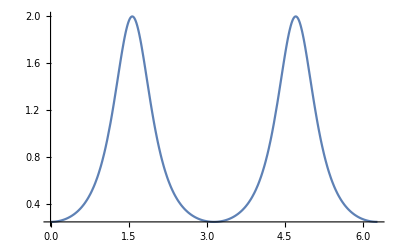

```mathematica
Plot[2/((4 Cos[t]^2+Sin[t]^2)^(3/2)),{t,0,2 π}]
```